# Quantized Random Walks

## 1-CDF of Unsigned Increments

Below is some code that plots 1-CDF of the random variable  variable Δ||u_t(||)^2 | u_(t-1). Below, w,σ represent the weight and ||u_(t-1)(||)_2, respectively. The gridlines in the plot demarcate the boundaries in the piecewise definition of the CDF -- namely, -w-w^2  and  w-w^2.
NOTE: it is assumed (for now) that w ≥ 0.

```mathematica
PlotTail[w_, σ_]:= Module[{d, P, A0, A1, Aneg1 , MyBound},
d = 2;
P[a_, b_]:= CDF[NormalDistribution[0,σ],b] -  CDF[NormalDistribution[0,σ],a];
A0[t_]:= Piecewise[{{0,t > Abs[w]-w^2}, {P[(t-w^2)/(2w), 1/2-w], t < Abs[w]-w^2 && t > -Abs[w]-w^2}, {P[-1/2-w, 1/2-w], t < -Abs[w]-w^2}}];
A1[t_]:= Piecewise[{{0, t > w - w^2},{P[1/2-w, (t-(w-1)^2)/(2(w-1))], t < w-w^2}}];
Aneg1[t_]:= Piecewise[{{0, t > -w - w^2},{P[ (t-w(w+2)-1)/(2(w+1)),-1/2-w], t < -w-w^2}}];
MyBound[t_]:=Piecewise[{{P[(t-(w+1)^2)/(2(w+1)), (t-(w-1)^2)/(2(w-1))], t < -w-w^2}, {P[(t-w^2)/(2 w), (t - (w-1)^2)/(2(w-1))] , t ≥ -w -w^2&& t ≤ w-w^2}, {0, t> w - w^2}}];
MyBound2[t_]:=Piecewise[{{P[(t-(w+1)^2)/(2(w+1)), (t-(w-1)^2)/(2(w-1))], t < -Abs[w]-w^2}, {P[ (t - (w-1)^2)/(2(w-1)),(t-w^2)/(2 w)] , t ≥ -Abs[w] -w^2&& t ≤ Abs[w]-w^2}, {0, t> Abs[w] - w^2}}];
Plot[ A0[t]+A1[t] +Aneg1[t], {t,-1/2,1/4},GridLines->{{-w-w^2, w-w^2},{0,0.5,1}}, PlotRange-> {-0.1,1} ]
(*Plot[{A0[t]+A1[t] + Aneg1[t], MyBound[t]}, {t,-2,2}, PlotRange-> {0,1} ]*)
(*Plot[MyBound[t], {t,-2,2}, PlotRange-> {0,1} ]*)
]
```

```mathematica
Manipulate[PlotTail[ w, σ], {w,0,1,0.05},{σ,0.1,10,0.1}]
```

## CDF of Absolute Square Increments

Below is some code that generates the CDF of the random variable |Δ||u_t(||)^2| | u_(t-1). Below, w,σ represent the weight and ||u_(t-1)(||)_2, respectively. The gridlines in the plot demarcate the boundaries in the piecewise definition of the CDF -- namely, w-w^2  and  w+w^2.
NOTE: it is assumed (for now) that w ≥ 0.

```mathematica
PlotAbsCDF[w_,σ_]:=Module[{P,Aneg1, A0, A1},
P[a_, b_]:= CDF[NormalDistribution[0,σ],b] -  CDF[NormalDistribution[0,σ],a];
Aneg1[α_]:= Piecewise[{
{0, α ≤  w+w^2},
{P[(-α-(w+1)^2)/(2(w+1)), -1/2-w],  α > w + w^2}
}];
A0[α_]:= Piecewise[{
{P[(-α - w^2)/(2w), (α-w^2)/(2w)], 0 ≤ α < w-w^2},
{P[(-α - w^2)/(2w), 1/2-w], w-w^2 ≤ α < w+w^2},
{P[-1/2-w, 1/2-w], α ≥ w+w^2}
}];
A1[α_]:= Piecewise[{
{P[(-α+(w-1)^2)/(2(1-w)), (α+(w-1)^2)/(2(1-w))], 0 ≤ α < w - w^2},
{P[1/2-w, (α+(w-1)^2)/(2(1-w))], w-w^2 ≤ α}
}];
MyCDF[α_]:= Aneg1[α] + A0[α] + A1[α];
Plot[1-MyCDF[α],{α,0,5}, PlotRange-> {0,1},GridLines->{{w-w^2, w+w^2},{0,0.5,1}}]
];
Manipulate[PlotAbsCDF[w,σ],{w,0.1,0.9},{σ,0.1,2}]
```

```mathematica
4*Exp[42/8]
```

4 ⅇ^(21/4)

```mathematica
N[%]
```

762.265

```mathematica
Simplify[(α+(w-1)^2)/(2(1-w)u)+(α+(w-1)^2)/(2(w+1)u)]
```

(1-2 w+w^2+α)/(u-u w^2)

## How Loose is Our Exponential Bound?

```mathematica
Manipulate[Plot[{(1-z^2)^((d-3)/2), Exp[-(d-3)/2 z^2]},{z,0,1}],{d,4,100}]
```

## Stereographically Projecting to the Sphere

Instead of assuming that our vectors are distributed on the sphere, we wonder how the geometry of the problem changes if we assume they are distributed according to some distribution over R^d. There, q_t= Q(w_t+X_t^T/(||X_t(||)^2)u_(t-1)). So, we wonder what the level sets of q_t look like. Below are some graphics which depict their behavior.

```mathematica
u = {1,0};
Manipulate[RegionPlot[{Norm[{x,y} - 1/(1-2w)u, 2]≤ 1/(1-2 w), Norm[{x,y} + 1/(1+2w)u, 2]≤ 1/(1+2 w)},{x,-5,5},{y,-5,5}, PlotLegends->{"{X_t : q_t = 1}", "{X_t: q_t=-1}"}],{w,-1/2+0.01,1/2-0.01}]
```

So it looks like these level sets “naturally’’ live on a sphere. Let’s stereographically project R^2 onto S^2 to see how these level sets behave there.

```mathematica
ψ[θ_,ϕ_]:= {(2 Cos[θ]Sin[ϕ])/(1 - Cos[ϕ]), (2Sin[θ]Sin[ϕ])/(1-Cos[ϕ])}(** Map from S^2 to R^2 **);
ψinverse[x_,y_]:= {(2x)/(1 + x^2+y^2),(2y)/(1 + x^2+y^2),(x^2+y^2-1)/(1+x^2+y^2)} (** Map from R^2 to S^2 **);
```

```mathematica
Manipulate[
Show[
ParametricPlot3D[{Cos[θ]Sin[ϕ],Sin[θ]Sin[ϕ],Cos[ϕ]},{θ,0,2π},{ϕ,0,π}, PlotStyle->Directive[Blue,Opacity[0.1]], Mesh-> None,PlotLegends->{"{X_t : q_t = 0}"}],ParametricPlot3D[ψinverse[1/(1-2w)u[[1]] +r Cos[θ],1/(1-2w) u[[2]] + r Sin[θ]],{r,0,1/(1-2w)Norm[u,2]}, {θ,0,2π},PlotStyle->Directive[Green,Opacity[0.5]], Mesh-> None,PlotLegends->{"{X_t : q_t = 1}"}],
ParametricPlot3D[ψinverse[-1/(1+2w)u[[1]] +r Cos[θ],-1/(1+2w) u[[2]] + r Sin[θ]],{r,0,1/(1+2w)Norm[u,2]}, {θ,0,2π},PlotStyle->Directive[Red,Opacity[0.5]], Mesh-> None, PlotLegends->{"{X_t : q_t = -1}"}]
],{w,-1/2+0.01,1/2-0.01}
]
```

ParametricPlot3D::plln: Limiting value 13.1579 Norm[u,2] in {r,0,Norm[u,2]/(1-2 FE`w$$13)} is not a machine-sized real number.

ParametricPlot3D::plln: Limiting value 0.519751 Norm[u,2] in {r,0,Norm[u,2]/(1+2 FE`w$$13)} is not a machine-sized real number.

ParametricPlot3D::plln: Limiting value 13.1579 Norm[u,2] in {r,0,Norm[u,2]/(1-2 FE`w$$13)} is not a machine-sized real number.

General::stop: Further output of ParametricPlot3D::plln will be suppressed during this calculation.

PlotRange::prng: Value of option PlotRange -> {{Automatic,Automatic},{Automatic,Automatic},{Automatic,Automatic}} is not All, Full, Automatic, a positive machine number, or an appropriate list of range specifications.

Show::gcomb: Could not combine the graphics objects in ….

PlotRange::prng: Value of option PlotRange -> {{Automatic,Automatic},{Automatic,Automatic},{Automatic,Automatic}} is not All, Full, Automatic, a positive machine number, or an appropriate list of range specifications.

Show::gcomb: Could not combine the graphics objects in ….

PlotRange::prng: Value of option PlotRange -> {{Automatic,Automatic},{Automatic,Automatic},{Automatic,Automatic}} is not All, Full, Automatic, a positive machine number, or an appropriate list of range specifications.

General::stop: Further output of PlotRange::prng will be suppressed during this calculation.

Show::gcomb: Could not combine the graphics objects in ….

General::stop: Further output of Show::gcomb will be suppressed during this calculation.

ParametricPlot3D::plln: Limiting value 13.1579 Norm[u,2] in {r,0,Norm[u,2]/(1-2 FE`w$$13)} is not a machine-sized real number.

ParametricPlot3D::plln: Limiting value 0.519751 Norm[u,2] in {r,0,Norm[u,2]/(1+2 FE`w$$13)} is not a machine-sized real number.

ParametricPlot3D::plln: Limiting value 13.1579 Norm[u,2] in {r,0,Norm[u,2]/(1-2 FE`w$$13)} is not a machine-sized real number.

General::stop: Further output of ParametricPlot3D::plln will be suppressed during this calculation.

PlotRange::prng: Value of option PlotRange -> {{Automatic,Automatic},{Automatic,Automatic},{Automatic,Automatic}} is not All, Full, Automatic, a positive machine number, or an appropriate list of range specifications.

Show::gcomb: Could not combine the graphics objects in ….

PlotRange::prng: Value of option PlotRange -> {{Automatic,Automatic},{Automatic,Automatic},{Automatic,Automatic}} is not All, Full, Automatic, a positive machine number, or an appropriate list of range specifications.

Show::gcomb: Could not combine the graphics objects in ….

PlotRange::prng: Value of option PlotRange -> {{Automatic,Automatic},{Automatic,Automatic},{Automatic,Automatic}} is not All, Full, Automatic, a positive machine number, or an appropriate list of range specifications.

General::stop: Further output of PlotRange::prng will be suppressed during this calculation.

Show::gcomb: Could not combine the graphics objects in ….

General::stop: Further output of Show::gcomb will be suppressed during this calculation.

ParametricPlot3D::plln: Limiting value 0.791139 Norm[u,2] in {r,0,Norm[u,2]/(1-2 FE`w$$13)} is not a machine-sized real number.

ParametricPlot3D::plln: Limiting value 1.3587 Norm[u,2] in {r,0,Norm[u,2]/(1+2 FE`w$$13)} is not a machine-sized real number.

ParametricPlot3D::plln: Limiting value 0.791139 Norm[u,2] in {r,0,Norm[u,2]/(1-2 FE`w$$13)} is not a machine-sized real number.

General::stop: Further output of ParametricPlot3D::plln will be suppressed during this calculation.

PlotRange::prng: Value of option PlotRange -> {{Automatic,Automatic},{Automatic,Automatic},{Automatic,Automatic}} is not All, Full, Automatic, a positive machine number, or an appropriate list of range specifications.

Show::gcomb: Could not combine the graphics objects in ….

PlotRange::prng: Value of option PlotRange -> {{Automatic,Automatic},{Automatic,Automatic},{Automatic,Automatic}} is not All, Full, Automatic, a positive machine number, or an appropriate list of range specifications.

Show::gcomb: Could not combine the graphics objects in ….

PlotRange::prng: Value of option PlotRange -> {{Automatic,Automatic},{Automatic,Automatic},{Automatic,Automatic}} is not All, Full, Automatic, a positive machine number, or an appropriate list of range specifications.

General::stop: Further output of PlotRange::prng will be suppressed during this calculation.

Show::gcomb: Could not combine the graphics objects in ….

General::stop: Further output of Show::gcomb will be suppressed during this calculation.

## Checking out The Bad MGF Integral

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

General::stop: Further output of NIntegrate::izero will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {3.73991}. NIntegrate obtained 2.0278×10^9 and 9251.58 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {3.57355}. NIntegrate obtained 2.14924×10^9 and 3841.03 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {3.22096}. NIntegrate obtained 2.36783×10^9 and 3788. for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

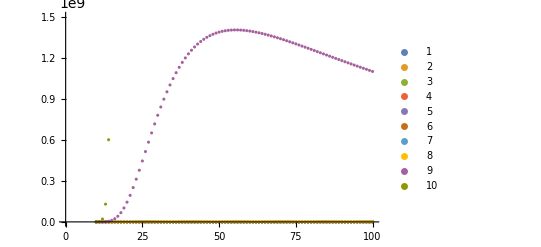

```mathematica
w = 0.25;
d = 100;
σ = 1;
λ = 1;
ListPlot[Table[{u,(2π σ^2)^(-1/2)NIntegrate[Exp[2λ w u x - x^2/(2 σ^2)]*(1-CDF[ChiSquareDistribution[d-1], σ^-2(2x u - x^2)]),{x,0,2u}]},{σ,1/Sqrt[d], 1,0.1},{u,Sqrt[d], d}], PlotLegends-> Automatic]
```

```mathematica
σ = 1/Sqrt[d];
Manipulate[Plot[(1-CDF[ChiSquareDistribution[d-1], σ^-2(2x u - x^2)]),{x,0,3u}],{u,1,10}]
```

```mathematica
d= 10;
Manipulate[Plot[(2π σ^2)^(-1/2)Exp[w/(d σ^2)]Exp[2/(d σ^2) w u x - x^2/(2 σ^2)]*(1-CDF[ChiSquareDistribution[d-1], σ^-2(2x u - x^2)]),{x,0,1}],{σ,1/d^2,10},{u,σ d,d^3}]
```